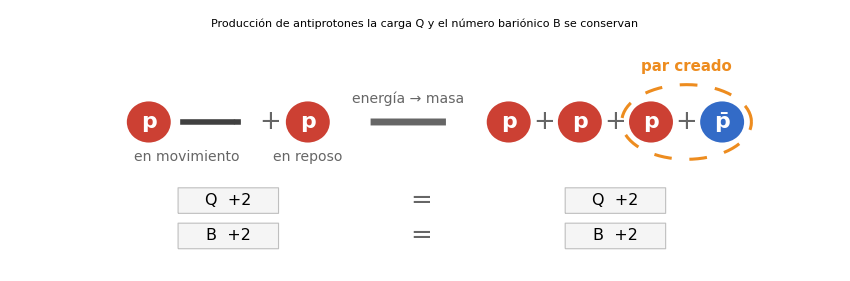

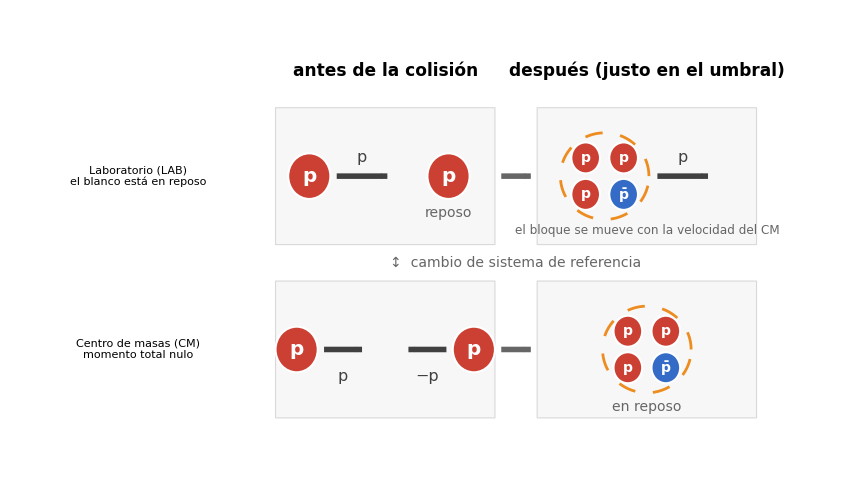

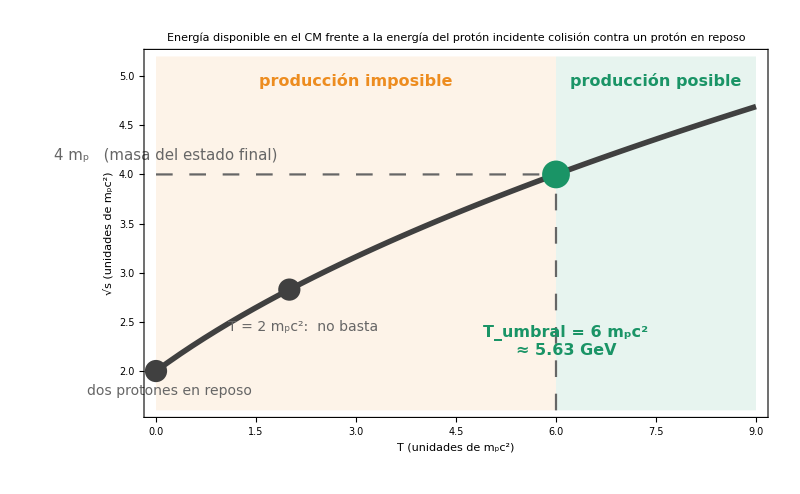

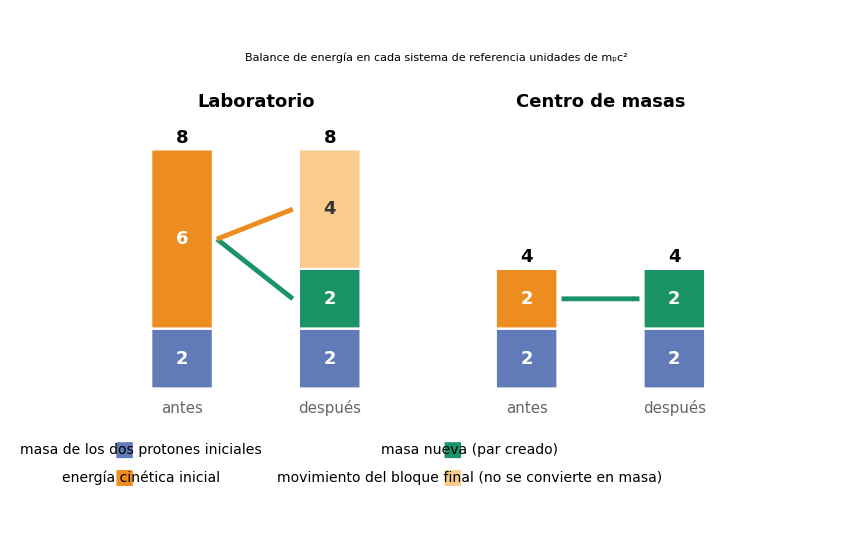

```mathematica
(* ==================================================================*)(*UMBRAL DE PRODUCCION DE ANTIPROTONES:p+p->p+p+p+pbar*)(*BoletinA_P3_a... BoletinA_P3_d*)(* ==================================================================*)ClearAll[bProt,bAnti,bMom,bCM,bNar,bNarClaro,bMasa,bGris,bDisco,bFlecha,bChip,chipC,fPa,bBloque,bCelda,fPb,fPc,barraE,fPd];

(*----------Paleta----------*)
bProt=RGBColor[0.80,0.25,0.20];     (*proton*)
bAnti=RGBColor[0.20,0.42,0.78];     (*antiproton*)
bMom=GrayLevel[0.25];                (*momentos*)
bCM=RGBColor[0.10,0.58,0.40];     (*masa nueva/centro de masas*)
bNar=RGBColor[0.93,0.55,0.12];     (*energia cinetica/par creado*)
bNarClaro=RGBColor[0.98,0.80,0.55];
bMasa=RGBColor[0.38,0.48,0.72];     (*masa en reposo inicial*)
bGris=GrayLevel[0.4];

(*----------Utilidades----------*)
bDisco[pos_,col_,t_,r_:0.45,fs_:18]:={{col,EdgeForm[{White,AbsoluteThickness[1.5]}],Disk[pos,r]},Text[Style[t,fs,Bold,White],pos]};

bFlecha[p_,q_,col_:GrayLevel[0.25],g_:3.5,h_:0.05]:={col,AbsoluteThickness[g],Arrowheads[h],Arrow[{p,q}]};

bChip[pos_,ancho_,alto_,txt_]:={{GrayLevel[0.96],EdgeForm[GrayLevel[0.75]],Rectangle[pos-{ancho,alto}/2,pos+{ancho,alto}/2,RoundingRadius->0.12]},Text[txt,pos]};

(* ==================================================================*)
(*BoletinA_P3_a-La reaccion y lo que se conserva*)
(* ==================================================================*)
chipC[x_,y_,nombre_,val_]:=bChip[{x,y},2.4,0.65,Style[Row[{Style[nombre<>"  ",bGris],Style[val,Bold,bProt]}],16]];

fPa=Graphics[{(*estado inicial*)bDisco[{1.7,3.6},bProt,"p",0.55,22],bFlecha[{2.45,3.6},{3.9,3.6},bMom,4,0.06],Text[Style["en movimiento",14,bGris],{2.6,2.7}],Text[Style["+",26,bGris],{4.6,3.6}],bDisco[{5.5,3.6},bProt,"p",0.55,22],Text[Style["en reposo",14,bGris],{5.5,2.7}],(*reaccion*)bFlecha[{7.0,3.6},{8.8,3.6},bGris,5,0.06],Text[Style["energía → masa",14,bGris],{7.9,4.2}],(*estado final*)MapThread[bDisco[{#1,3.6},#2,#3,0.55,22]&,{{10.3,12.0,13.7,15.4},{bProt,bProt,bProt,bAnti},{"p","p","p",OverBar["p"]}}],Table[Text[Style["+",26,bGris],{x,3.6}],{x,{11.15,12.85,14.55}}],(*par creado*){bNar,Dashing[{0.015,0.015}],AbsoluteThickness[2.2],Circle[{14.55,3.6},{1.55,0.95}]},Text[Style["par creado",15,Bold,bNar],{14.55,5.0}],(*cantidades conservadas*)chipC[3.6,1.6,"Q","+2"],chipC[12.85,1.6,"Q","+2"],chipC[3.6,0.7,"B","+2"],chipC[12.85,0.7,"B","+2"],Text[Style["=",26,bGris],{8.2,1.6}],Text[Style["=",26,bGris],{8.2,0.7}]},PlotRange->{{0,16.6},{0.2,5.7}},PlotRangePadding->None,ImageSize->850,PlotLabel->Column[{Style["Producción de antiprotones",20,Bold],Style["la carga Q y el número bariónico B se conservan",15,bGris]},Center]];

(* ==================================================================*)
(*BoletinA_P3_b-Los dos sistemas de referencia*)
(* ==================================================================*)
(*bloque de 4 particulas (3 p+1 pbar) que salen juntas en el umbral*)
bBloque[c_]:={{bNar,Dashing[{0.015,0.015}],AbsoluteThickness[2],Circle[c,{1.05,0.95}]},bDisco[c+{-0.45,0.4},bProt,"p",0.34,14],bDisco[c+{0.45,0.4},bProt,"p",0.34,14],bDisco[c+{-0.45,-0.4},bProt,"p",0.34,14],bDisco[c+{0.45,-0.4},bAnti,OverBar["p"],0.34,14]};

bCelda[c_]:={GrayLevel[0.97],EdgeForm[GrayLevel[0.85]],Rectangle[c-{2.6,1.5},c+{2.6,1.5},RoundingRadius->0.15]};

fPb=Graphics[{(*cabeceras*)Text[Style["antes de la colisión",17,Bold],{6.0,8.3}],Text[Style["después (justo en el umbral)",17,Bold],{12.2,8.3}],(*celdas*)Table[bCelda[{x,y}],{x,{6.0,12.2}},{y,{6.0,2.2}}],(*etiquetas de fila*)Text[Column[{Style["Laboratorio (LAB)",17,Bold],Style["el blanco está en reposo",13,bGris]},Left],{0.15,6.0},{-1,0}],Text[Column[{Style["Centro de masas (CM)",17,Bold],Style["momento total nulo",13,bGris]},Left],{0.15,2.2},{-1,0}],(*LAB,antes:proyectil y blanco en reposo*)bDisco[{4.2,6.0},bProt,"p",0.5,20],bFlecha[{4.85,6.0},{6.05,6.0},bMom,4,0.06],Text[Style["p",16,bMom],{5.45,6.4}],bDisco[{7.5,6.0},bProt,"p",0.5,20],Text[Style["reposo",14,bGris],{7.5,5.2}],(*LAB,despues:el bloque conserva el momento total*)bBloque[{11.2,6.0}],bFlecha[{12.45,6.0},{13.65,6.0},bMom,4,0.06],Text[Style["p",16,bMom],{13.05,6.4}],Text[Style["el bloque se mueve con la velocidad del CM",12,bGris],{12.2,4.8}],(*CM,antes:momentos iguales y opuestos*)bDisco[{3.9,2.2},bProt,"p",0.5,20],bFlecha[{4.55,2.2},{5.45,2.2},bMom,4,0.07],bDisco[{8.1,2.2},bProt,"p",0.5,20],bFlecha[{7.45,2.2},{6.55,2.2},bMom,4,0.07],Text[Style["p",16,bMom],{5.0,1.6}],Text[Style["−p",16,bMom],{7.0,1.6}],(*CM,despues:todo en reposo*)bBloque[{12.2,2.2}],Text[Style["en reposo",14,bGris],{12.2,0.95}],(*transiciones*)bFlecha[{8.75,6.0},{9.45,6.0},bGris,4,0.1],bFlecha[{8.75,2.2},{9.45,2.2},bGris,4,0.1],Text[Style["↕  cambio de sistema de referencia",14,bGris],{9.1,4.1}]},PlotRange->{{0,15.2},{0.3,8.9}},PlotRangePadding->None,ImageSize->850];

(* ==================================================================*)
(*BoletinA_P3_c-Por que hacen falta 6 m_p c^2 de energia cinetica*)
(* ==================================================================*)
fPc=Plot[Sqrt[4+2 t],{t,0,9},PlotStyle->{bMom,AbsoluteThickness[4]},PlotRange->{{0,9},{1.6,5.2}},PlotRangePadding->None,Frame->True,FrameStyle->Directive[GrayLevel[0.25],14],FrameLabel->{Style[Row[{"T   (unidades de ",Subscript["m","p"],Superscript["c",2],")"}],16],Style[Row[{Sqrt["s"],"   (unidades de ",Subscript["m","p"],Superscript["c",2],")"}],16]},ImageSize->800,PlotLabel->Column[{Style["Energía disponible en el CM frente a la energía del protón incidente",19,Bold],Style["colisión contra un protón en reposo",15,bGris]},Center],Prolog->{{bNar,Opacity[0.10],Rectangle[{0,1.6},{6,5.2}]},{bCM,Opacity[0.10],Rectangle[{6,1.6},{9,5.2}]}},Epilog->{{bGris,Dashing[{0.015,0.015}],AbsoluteThickness[1.6],Line[{{0,4},{6,4}}],Line[{{6,1.6},{6,4}}]},{bCM,PointSize[0.025],Point[{6,4}]},{bMom,PointSize[0.02],Point[{0,2}],Point[{2,Sqrt[8]}]},Text[Style[Row[{"4 ",Subscript["m","p"],"   (masa del estado final)"}],15,bGris],{0.15,4.2},{-1,0}],Text[Style["dos protones en reposo",14,bGris],{0.2,1.8},{-1,0}],Text[Style[Row[{"T = 2 ",Subscript["m","p"],Superscript["c",2],":  no basta"}],14,bGris],{2.2,2.45},{-1,0}],Text[Style[Column[{Row[{"T",Subscript["","umbral"]," = 6 ",Subscript["m","p"],Superscript["c",2]}],"≈ 5.63 GeV"},Left],16,Bold,bCM],{6.15,2.3},{-1,0}],Text[Style["producción imposible",16,Bold,bNar],{3.0,4.95}],Text[Style["producción posible",16,Bold,bCM],{7.5,4.95}]}];

(* ==================================================================*)
(*BoletinA_P3_d-Balance de energia en LAB y CM (unidades de m_p c^2)*)
(* ==================================================================*)
(*segs={{valor,color,colorTexto},...} de abajo hacia arriba;1 unidad=0.75 de altura*)
barraE[x_,segs_List]:=Module[{bases=Most[Prepend[Accumulate[segs[[All,1]]],0]]},MapThread[Function[{s,b},If[s[[1]]>0,{{s[[2]],EdgeForm[{White,AbsoluteThickness[1.5]}],Rectangle[{x-0.75,0.75 b},{x+0.75,0.75 (b+s[[1]])}]},Text[Style[ToString[s[[1]]],18,Bold,s[[3]]],{x,0.75 (b+s[[1]]/2)}]},{}]],{segs,bases}]];

fPd=Graphics[{(*LAB*)barraE[2.0,{{2,bMasa,White},{6,bNar,White}}],barraE[5.6,{{2,bMasa,White},{2,bCM,White},{4,bNarClaro,GrayLevel[0.2]}}],bFlecha[{2.85,3.75},{4.7,2.25},bCM,3.5,0.045],bFlecha[{2.85,3.75},{4.7,4.5},bNar,3.5,0.045],Text[Style["8",18,Bold],{2.0,6.3}],Text[Style["8",18,Bold],{5.6,6.3}],Text[Style["antes",15,bGris],{2.0,-0.5}],Text[Style["después",15,bGris],{5.6,-0.5}],Text[Style["Laboratorio",18,Bold],{3.8,7.2}],(*CM*)barraE[10.4,{{2,bMasa,White},{2,bNar,White}}],barraE[14.0,{{2,bMasa,White},{2,bCM,White}}],bFlecha[{11.25,2.25},{13.15,2.25},bCM,3.5,0.045],Text[Style["4",18,Bold],{10.4,3.3}],Text[Style["4",18,Bold],{14.0,3.3}],Text[Style["antes",15,bGris],{10.4,-0.5}],Text[Style["después",15,bGris],{14.0,-0.5}],Text[Style["Centro de masas",18,Bold],{12.2,7.2}],(*leyenda*){bMasa,Rectangle[{0.4,-1.75},{0.8,-1.35}]},Text[Style["masa de los dos protones iniciales",14],{1.0,-1.55},{-1,0}],{bCM,Rectangle[{8.4,-1.75},{8.8,-1.35}]},Text[Style["masa nueva (par creado)",14],{9.0,-1.55},{-1,0}],{bNar,Rectangle[{0.4,-2.45},{0.8,-2.05}]},Text[Style["energía cinética inicial",14],{1.0,-2.25},{-1,0}],{bNarClaro,Rectangle[{8.4,-2.45},{8.8,-2.05}]},Text[Style["movimiento del bloque final (no se convierte en masa)",14],{9.0,-2.25},{-1,0}]},PlotRange->{{0,16.4},{-2.9,7.8}},PlotRangePadding->None,ImageSize->850,PlotLabel->Column[{Style["Balance de energía en cada sistema de referencia",20,Bold],Style[Row[{"unidades de ",Subscript["m","p"],Superscript["c",2]}],15,bGris]},Center]];

(*----------Mostrar----------*)
Print[fPa];Print[fPb];Print[fPc];Print[fPd];
```

```mathematica
(*----------Exportar----------*)
Export["BoletinA_P3_a.png",fPa,"PNG",Background->None,ImageResolution->300,ImageSize->850];
Export["BoletinA_P3_b.png",fPb,"PNG",Background->None,ImageResolution->300,ImageSize->850];
Export["BoletinA_P3_c.png",fPc,"PNG",Background->None,ImageResolution->300,ImageSize->800];
Export["BoletinA_P3_d.png",fPd,"PNG",Background->None,ImageResolution->300,ImageSize->850];
```

```mathematica
(* ==================================================================*)
(*DEUTERON EN UN POZO ESFERICO:V=-V0 (r<=a),0 (r>a)*)(*BoletinA_P4_a... BoletinA_P4_d*)
(* ==================================================================*)ClearAll[hc,mp,mn,mu,hm,aP,Bd,kP,xiP,alP,V0,V0min,etaP,Rx,pI,pII,pPot,pGris,panelGeom,panelNivel,fQa,fQb,fQc,topU,botV,fQd];

(*----------Datos y solucion exacta (para dibujar curvas coherentes)----------*)
hc=197.327;mp=938.272;mn=939.565;     (*hc en MeV fm;masas en MeV*)
mu=mp mn/(mp+mn);                           (*masa reducida n-p*)
hm=hc^2/(2 mu);                               (*hbar^2/(2 mu)=41.47 MeV fm^2*)
aP=1.59;Bd=2.224566;                      (*alcance del pozo (fm),energia de ligadura (MeV)*)
kP=Sqrt[Bd/hm];                               (*constante de atenuacion externa (1/fm)*)
xiP=xx/. FindRoot[xx/Tan[xx]+kP aP==0,{xx,1.8}];   (*alpha a:solucion exacta*)
alP=xiP/aP;                                   (*alpha*)
etaP=kP aP;                                   (*k a*)
Rx=Sqrt[xiP^2+etaP^2];                      (*"radio" que mide la profundidad del pozo*)
V0=Bd+hm alP^2;                             (*profundidad exacta*)
V0min=hm (Pi/(2 aP))^2;                       (*estimacion:alpha a=Pi/2*)
(*----------Paleta----------*)
pI=RGBColor[0.15,0.35,0.75];     (*u interior:seno*)
pII=RGBColor[0.10,0.58,0.40];     (*u exterior:exponencial*)
pPot=RGBColor[0.93,0.55,0.12];     (*potencial/pozo*)
pGris=GrayLevel[0.4];
```

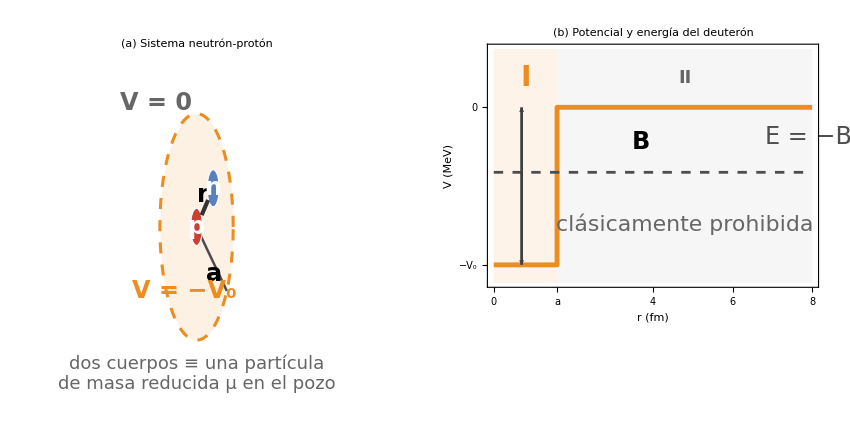

```mathematica
(* ==================================================================*)
(*BoletinA_P4_a-El sistema n-p y el pozo*)
(* ==================================================================*)
panelGeom=Graphics[{{pPot,Opacity[0.12],Disk[{0,0},2.2]},{pPot,Dashing[{0.02,0.02}],AbsoluteThickness[2.2],Circle[{0,0},2.2]},
(*radio del pozo*)
{GrayLevel[0.3],AbsoluteThickness[1.8],Line[{{0,0},2.2 {Cos[-0.6],Sin[-0.6]}}]},
Text[Style["a",24,Bold],1.1 {Cos[-0.6],Sin[-0.6]}+{0.15,-0.3}],
(*proton,neutron y coordenada relativa*)
{RGBColor[0.80,0.25,0.20],EdgeForm[White],Disk[{0,0},0.36]},Text[Style["p",24,Bold,White],{0,0}],{RGBColor[0.35,0.50,0.75],EdgeForm[White],Disk[{1.0,0.75},0.36]},
Text[Style["n",24,Bold,White],{1.0,0.75}],{GrayLevel[0.2],AbsoluteThickness[3],Arrowheads[0.07],Arrow[{{0.304,0.228},{0.696,0.522}}]},
Text[Style["r",24,Bold],{0.38,0.62}],
(*valores del potencial*)
Text[Style[Row[{"V = −",Subscript["V",0]}],24,Bold,pPot],{-0.75,-1.25}],Text[Style["V = 0",24,Bold,pGris],{-2.45,2.4}],
Text[Style[Column[{"dos cuerpos ≡ una partícula","de masa reducida μ en el pozo"},Center],18,pGris],{0,-2.85}]},
PlotRange->{{-3.4,3.4},{-3.4,3.2}},
PlotRangePadding->None,
ImageSize->400,
PlotLabel->Style["(a) Sistema neutrón-protón",20,Bold]];

Vprint=V0/10;
panelNivel=Graphics[
{
{pPot,Opacity[0.10],Rectangle[{0,-6},{aP,2}]},
{GrayLevel[0.5],Opacity[0.07],Rectangle[{aP,-6},{8,2}]},
(*potencial y nivel de energia*)
{pPot,AbsoluteThickness[3.5],Line[{{0,-Vprint},{aP,-Vprint},{aP,0},{8,0}}]},
{GrayLevel[0.3],Dashing[{0.015,0.015}],AbsoluteThickness[2],Line[{{0,-Bd},{8,-Bd}}]},
Text[Style["E = −B",24,GrayLevel[0.3]],{7.9,-1},{1,0}],
(*V0 y B*)
{GrayLevel[0.25],AbsoluteThickness[2],Arrowheads[{-0.03,0.03}],Arrow[{{0.7,-Vprint},{0.7,0}}]},Text[Style[Subscript["V",0],17,Bold],{0.85,-28},{-1,0}],Text[Style["B",24,Bold],{3.7,-1.2},{-1,0}],
(*zonas*)
Text[Style["I",28,Bold,pPot],{aP/2,1}],Text[Style["II",18,Bold,pGris],{4.8,1}],Text[Style["clásicamente prohibida",22,pGris],{4.8,-4}]
},
Frame->True,FrameStyle->Directive[GrayLevel[0.25],24],
FrameLabel->{Style["r  (fm)",24],Style["V  (MeV)",24]},
FrameTicks->{{{{0,"0"},{-Vprint,Row[{"−",Subscript["V",0]}]}},None},{{{0,"0"},{aP,"a"},{4,"4"},{6,"6"},{8,"8"}},None}},
PlotRange->{{0,8},{-6,2}},
PlotRangePadding->None,
ImageSize->450,
PlotLabel->Style["(b) Potencial y energía del deuterón",20,Bold]
];

fQa=GraphicsRow[{panelGeom,panelNivel},Spacings->15,ImageSize->850]
```

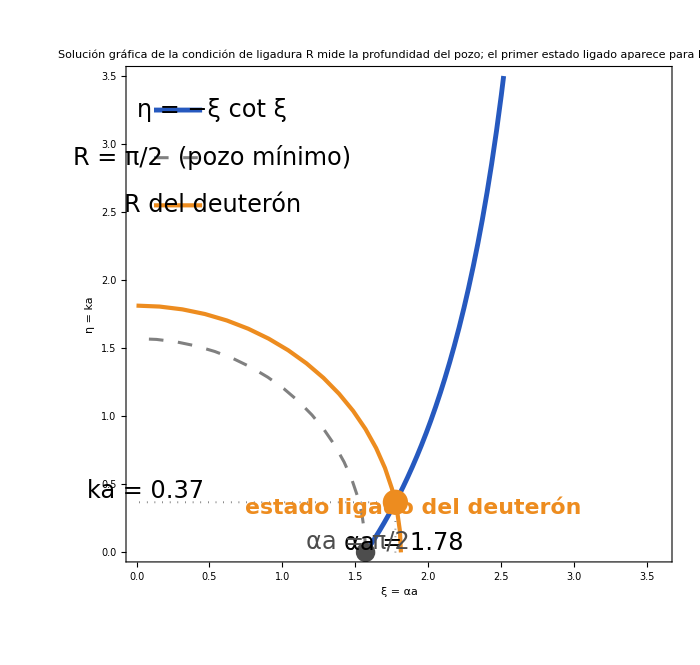

```mathematica
(* ==================================================================*)
(*BoletinA_P4_b-Solucion grafica de la condicion de ligadura*)
(*eta=-xi cot(xi)  (curva)   frente a   xi^2+eta^2=R^2*)
(* ==================================================================*)
fQb=Plot[-x/Tan[x],{x,Pi/2+0.001,Pi-0.001},
PlotStyle->{pI,AbsoluteThickness[3.5]},
PlotRange->{{0,3.6},{0,3.5}},
PlotRangePadding->None,Frame->True,
FrameStyle->Directive[GrayLevel[0.25],24],
FrameLabel->{Style[Row[{"ξ = αa"}],24],
Style[Row[{"η = ka"}],24]},
AspectRatio->0.95,
ImageSize->700,
PlotLabel->Column[{Style["Solución gráfica de la condición de ligadura",24,Bold],Style["R mide la profundidad del pozo; el primer estado ligado aparece para R > π/2",18,pGris]},Center],
Epilog->{
(*circunferencias*)
{GrayLevel[0.5],Dashing[{0.015,0.015}],AbsoluteThickness[2.2],Circle[{0,0},Pi/2,{0,Pi/2}]},{pPot,AbsoluteThickness[3],Circle[{0,0},Rx,{0,Pi/2}]},

(*solucion del deuteron*)

{GrayLevel[0.35],Dotted,AbsoluteThickness[1.4],Line[{{xiP,0},{xiP,etaP},{0,etaP}}]},{pPot,PointSize[0.026],Point[{xiP,etaP}]},
{GrayLevel[0.3],PointSize[0.02],Point[{Pi/2,0}]},Text[Style[Row[{"αa = ",NumberForm[xiP,{3,2}]}],24],{xiP+0.06,0.07},{-1,0}],
Text[Style[Row[{"ka = ",NumberForm[etaP,{3,2}]}],24],{0.06,etaP+0.08},{-1,0}],
Text[Style["estado ligado del deuterón",22,Bold,pPot],{xiP+0.12,0.33},{-1,0}],
Text[Style[Row[{"αa = π/2"}],24,GrayLevel[0.3]],{Pi/2-0.05,0.08},{1,0}],
(*leyenda*)
{pI,AbsoluteThickness[3.5],Line[{{0.12,3.25},{0.45,3.25}}]},
Text[Style[Row[{"η = −ξ cot ξ"}],24],{0.52,3.25},{-1,0}],
{GrayLevel[0.5],Dashing[{0.015,0.015}],AbsoluteThickness[2.2],
Line[{{0.12,2.9},{0.45,2.9}}]},
Text[Style["R = π/2  (pozo mínimo)",24],{0.52,2.9},{-1,0}],{pPot,AbsoluteThickness[3],
Line[{{0.12,2.55},{0.45,2.55}}]},
Text[Style["R del deuterón",24],{0.52,2.55},{-1,0}]
}
]
```

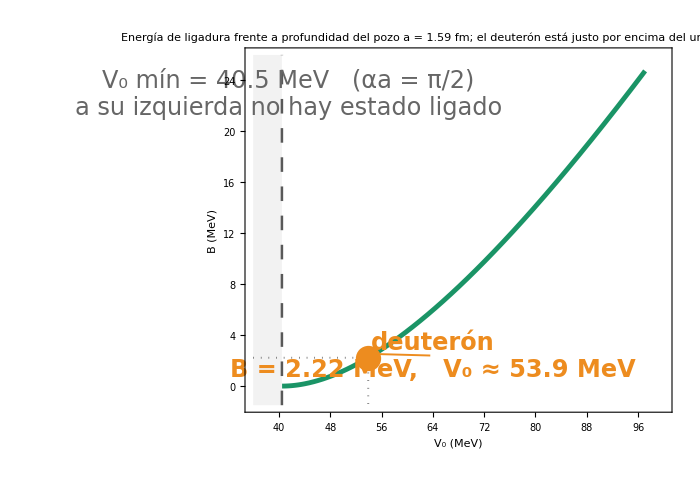

```mathematica
(* ==================================================================*)
(*BoletinA_P4_c-B en funcion de V0:el deuteron esta cerca del umbral*)
(* ==================================================================*)
fQc=ParametricPlot[{hm (xx^2+(xx/Tan[xx])^2)/aP^2,hm (xx/Tan[xx])^2/aP^2},{xx,Pi/2+0.0005,2.1},PlotStyle->{pII,AbsoluteThickness[3.5]},PlotRange->{{36,100},{-1.5,26}},
PlotRangePadding->None,
Frame->True,
FrameStyle->Directive[GrayLevel[0.25],14],
FrameLabel->{Style[Row[{Subscript["V",0],"   (MeV)"}],24],Style["B   (MeV)",24]},
AspectRatio->0.7,
ImageSize->700,PlotLabel->Column[{Style["Energía de ligadura frente a profundidad del pozo",24,Bold],Style[Row[{"a = ",aP," fm;  el deuterón está justo por encima del umbral de ligadura"}],20,pGris]},Center],Prolog->{GrayLevel[0.5],Opacity[0.10],Rectangle[{36,-1.5},{V0min,26}]},
Epilog->{
{GrayLevel[0.35],Dashing[{0.015,0.015}],AbsoluteThickness[1.8],
Line[{{V0min,-1.5},{V0min,26}}]},Text[Style[Column[{Row[{Subscript["V",0]," mín = ",NumberForm[V0min,{3,1}]," MeV   (αa = π/2)"}],"a su izquierda no hay estado ligado"},Left],24,pGris],{41.5,23},{-1,0}],{GrayLevel[0.35],Dotted,AbsoluteThickness[1.4],Line[{{36,Bd},{V0,Bd},{V0,-1.5}}]},{pPot,PointSize[0.026],Point[{V0,Bd}]},{pPot,AbsoluteThickness[1.4],Line[{{V0+0.8,Bd+0.3},{63.6,2.4}}]},
Text[Style[Column[{"deuterón",Row[{"B = ",NumberForm[Bd,{3,2}]," MeV,   ",Subscript["V",0]," ≈ ",NumberForm[V0,{3,1}]," MeV"}]},Left],24,Bold,pPot],{64,2.4},{-1,0}]
}
]
```

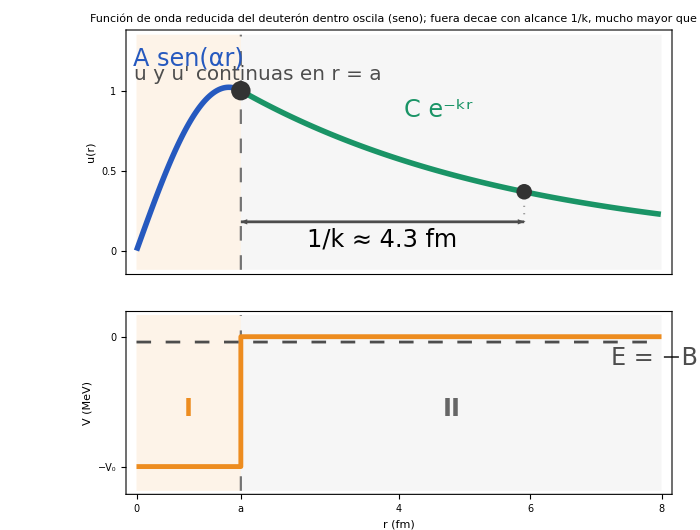

```mathematica
(* ==================================================================*)
(*BoletinA_P4_d-Funcion de onda reducida u(r) y potencial*)
(* ==================================================================*)
topU=Graphics[{
{pPot,Opacity[0.10],Rectangle[{0,-0.12},{aP,1.35}]},{GrayLevel[0.5],Opacity[0.07],Rectangle[{aP,-0.12},{8,1.35}]},{GrayLevel[0.45],Dashing[{0.015,0.015}],AbsoluteThickness[1.6],Line[{{aP,-0.12},{aP,1.35}}]},

(*u(r):seno dentro,exponencial fuera,empalmadas con u(a)=1*)

{pI,AbsoluteThickness[4],Line[Table[{r,Sin[alP r]/Sin[xiP]},{r,0,aP,aP/60}]]},{pII,AbsoluteThickness[4],Line[Table[{r,Exp[-kP (r-aP)]},{r,aP,8,0.05}]]},{GrayLevel[0.2],PointSize[0.02],Point[{aP,1}]},Text[Style["u y u' continuas en r = a",20,GrayLevel[0.3]],{1.85,1.1},{-1,0}],
Text[Style[Row[{"A sen(","α","r)"}],24,pI],{aP/2,1.2}],
Text[Style[Row[{"C ",Superscript["e",Row[{"−kr"}]]}],24,pII],{4.6,0.88}],
(*alcance de la cola:1/k*)
{GrayLevel[0.3],AbsoluteThickness[2],Arrowheads[{-0.03,0.03}],Arrow[{{aP,0.18},{aP+1/kP,0.18}}]},
{GrayLevel[0.3],Dotted,AbsoluteThickness[1.4],Line[{{aP+1/kP,0.18},{aP+1/kP,Exp[-1]}}]},
{GrayLevel[0.2],PointSize[0.016],Point[{aP+1/kP,Exp[-1]}]},Text[Style[Row[{"1/k ≈ ",NumberForm[1/kP,{2,1}]," fm"}],24],{aP+1/(2 kP),0.07}]
},
Frame->True,
FrameStyle->Directive[GrayLevel[0.25],24],
FrameLabel->{{Style["u(r)",24],None},{None,None}},
FrameTicks->{{{{0,"0"},{0.5,"0.5"},{1,"1"}},None},{Table[{x,""},{x,{0,2,4,6,8}}],None}},
PlotRange->{{0,8},{-0.12,1.35}},
PlotRangePadding->None,
ImagePadding->{{70,25},{10,40}},
ImageSize->{700,300},
AspectRatio->Full,
PlotLabel->Column[{Style["Función de onda reducida del deuterón",24,Bold],Style["dentro oscila (seno); fuera decae con alcance 1/k, mucho mayor que a",18,pGris]},Center]
];

botV=Graphics[
{
{pPot,Opacity[0.10],Rectangle[{0,-64},{aP,9}]},
{GrayLevel[0.5],Opacity[0.07],Rectangle[{aP,-64},{8,9}]},
{GrayLevel[0.45],Dashing[{0.015,0.015}],AbsoluteThickness[1.6],Line[{{aP,-64},{aP,9}}]},
{pPot,AbsoluteThickness[3.5],Line[{{0,-V0},{aP,-V0},{aP,0},{8,0}}]},
{GrayLevel[0.3],Dashing[{0.015,0.015}],AbsoluteThickness[2],Line[{{0,-Bd},{8,-Bd}}]},
Text[Style["E = −B",24,GrayLevel[0.3]],{7.9,-9},{1,0}],
Text[Style["I",24,Bold,pPot],{aP/2,-30}],
Text[Style["II",24,Bold,pGris],{4.8,-30}]
},
Frame->True,
FrameStyle->Directive[GrayLevel[0.25],24],
FrameLabel->{{Style["V  (MeV)",24],None},{Style["r  (fm)",24],None}},
FrameTicks->{{{{0,"0"},{-V0,Row[{"−",Subscript["V",0]}]}},None},{{{0,"0"},{aP,"a"},{4,"4"},{6,"6"},{8,"8"}},None}},
PlotRange->{{0,8},{-64,9}},
PlotRangePadding->None,
ImagePadding->{{70,25},{70,8}},
ImageSize->{700,230},
AspectRatio->Full];

fQd=GraphicsColumn[{topU,botV},Spacings->0,ImageSize->700]
```

```mathematica
(*----------Exportar----------*)
Export["BoletinA_P4_a.png",fQa,"PNG",Background->None,ImageResolution->300,ImageSize->850];
Export["BoletinA_P4_b.png",fQb,"PNG",Background->None,ImageResolution->300,ImageSize->700];
Export["BoletinA_P4_c.png",fQc,"PNG",Background->None,ImageResolution->300,ImageSize->700];
Export["BoletinA_P4_d.png",fQd,"PNG",Background->None,ImageResolution->300,ImageSize->700];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["BoletinA_P4_a.png"]]]
```

```mathematica
(* ==================================================================*)(*ACOPLAMIENTO DE MOMENTOS ANGULARES Y SIMETRIA DE ESPIN*)(*BoletinA_P12_a... BoletinA_P12_d*)(* ==================================================================*)ClearAll[eL,eS,eJ,eT,eSim,eAnt,eGris,vecTri,fMa,ketTxt,probTxt,cajaK,cols,fMb,bloqueS,resumenS,fMc,celdaRegla,fMd];
(*----------Paleta----------*)
eL=RGBColor[0.10,0.58,0.40];     (*momento angular orbital L*)
eS=RGBColor[0.93,0.55,0.12];     (*espin S*)
eJ=GrayLevel[0.15];                (*momento angular total J*)
eT=RGBColor[0.15,0.35,0.75];     (*tetraplete*)
eSim=RGBColor[0.25,0.65,0.35];     (*simetrico*)
eAnt=RGBColor[0.55,0.25,0.65];     (*antisimetrico*)
eGris=GrayLevel[0.4];
```

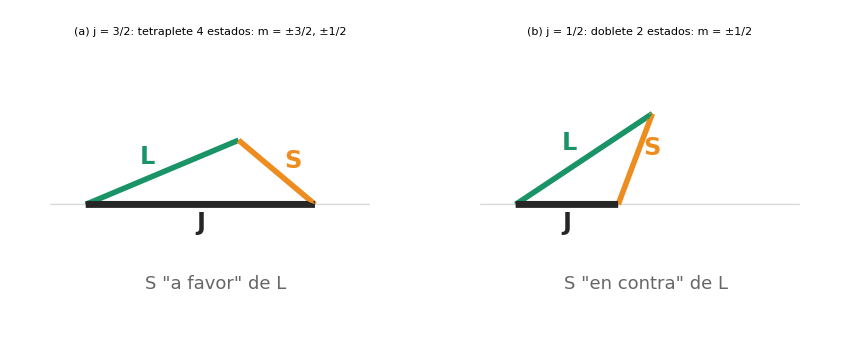

```mathematica
(* ==================================================================*)
(*BoletinA_P12_a-Modelo vectorial:l=1 y s=1/2->j=3/2,1/2*)
(* ==================================================================*)
vecTri[Lm_,Sm_,Jm_,titulo_,sub_,nota_]:=Module[{th,Lv,Jv,Sv},th=ArcCos[(Jm^2+Lm^2-Sm^2)/(2 Jm Lm)];
Jv={Jm,0};Lv=Lm {Cos[th],Sin[th]};Sv=Jv-Lv;
Graphics[{
{GrayLevel[0.85],AbsoluteThickness[1],Line[{{-0.3,0},{2.4,0}}]},
{eL,AbsoluteThickness[4],Arrowheads[0.05],Arrow[{{0,0},Lv}]},
{eS,AbsoluteThickness[4],Arrowheads[0.05],Arrow[{Lv,Jv}]},
{eJ,AbsoluteThickness[5],Arrowheads[0.05],Arrow[{{0,0},Jv}]},
Text[Style["L",24,Bold,eL],Lv/2+{-0.12,0.14}],Text[Style["S",24,Bold,eS],Lv+Sv/2+{0.14,0.1}],Text[Style["J",24,Bold,eJ],Jv/2+{0,-0.17}],Text[Style[nota,18,eGris],{1.1,-0.72}]
},
PlotRange->{{-0.4,2.5},{-1.0,1.4}},PlotRangePadding->None,ImageSize->425,PlotLabel->Column[{Style[titulo,24,Bold],Style[sub,20,eGris]},Center]]];


fMa=GraphicsRow[
{
vecTri[N[Sqrt[2]],N[Sqrt[3]/2],N[Sqrt[15]/2],"(a)  j = 3/2:  tetraplete","4 estados:  m = ±3/2, ±1/2","S \"a favor\" de L"],
vecTri[N[Sqrt[2]],N[Sqrt[3]/2],N[Sqrt[3]/2],"(b)  j = 1/2:  doblete","2 estados:  m = ±1/2","S \"en contra\" de L"]
},
Spacings->10,ImageSize->850]
```

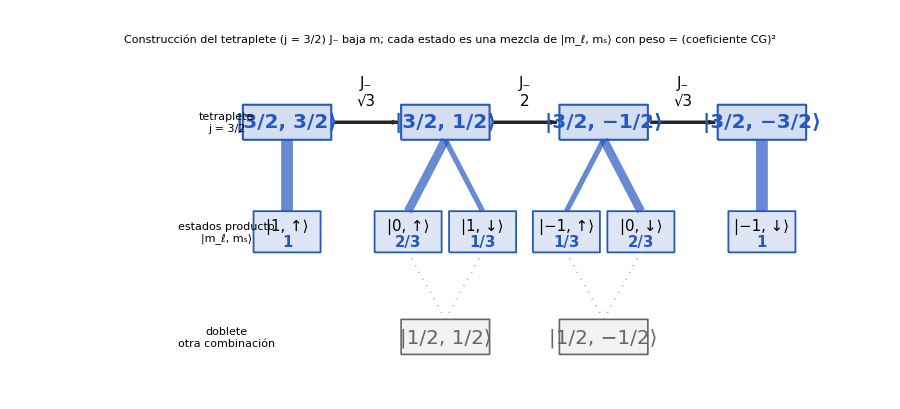

```mathematica
(* ==================================================================*)
(*BoletinA_P12_b-Construccion del tetraplete con J-*)
(* ==================================================================*)
ketTxt[ml_,ms_]:=Row[{"|",If[ml<0,"−"<>ToString[-ml],ToString[ml]],", ",If[ms>0,"↑","↓"],"⟩"}];

probTxt[p_]:=If[p==1,"1",ToString[Numerator[p]]<>"/"<>ToString[Denominator[p]]];

cajaK[x_,y_,ml_,ms_,p_]:={{Lighter[eT,0.85],EdgeForm[{eT,AbsoluteThickness[1.3]}],Rectangle[{x-0.72,y-0.47},{x+0.72,y+0.47},RoundingRadius->0.1]},Text[Style[ketTxt[ml,ms],15],{x,y+0.14}],Text[Style[probTxt[p],15,Bold,eT],{x,y-0.22}]};

(*{posicion x,m_j,{{m_l,m_s,peso=CG^2},...}}*)
cols={{1.6,"3/2",{{1,1/2,1}}},{5.0,"1/2",{{0,1/2,2/3},{1,-1/2,1/3}}},{8.4,"−1/2",{{-1,1/2,1/3},{0,-1/2,2/3}}},{11.8,"−3/2",{{-1,-1/2,1}}}};

fMb=Graphics[{(*estados del tetraplete*)Table[With[{c=cols[[i]]},{{Lighter[eT,0.8],EdgeForm[{eT,AbsoluteThickness[1.5]}],Rectangle[{c[[1]]-0.95,5.4},{c[[1]]+0.95,6.2},RoundingRadius->0.12]},Text[Style[Row[{"|3/2, ",c[[2]],"⟩"}],20,Bold,eT],{c[[1]],5.8}]}],{i,4}],(*operador de descenso*)Table[With[{x1=cols[[i,1]]+1.0,x2=cols[[i+1,1]]-1.0,co={Sqrt[3],2,Sqrt[3]}[[i]]},{{eJ,AbsoluteThickness[2.5],Arrowheads[0.06],Arrow[{{x1,5.8},{x2,5.8}}]},Text[Style[Column[{Subscript["J","−"],co},Center],15],{(x1+x2)/2,6.5}]}],{i,3}],(*composicion:grosor de la linea=peso*)Table[With[{c=cols[[i]],n=Length[cols[[i,3]]]},Table[With[{b=c[[3,j]],xb=c[[1]]+If[n==1,0,(2 j-3) 0.8]},{eT,Opacity[0.7],AbsoluteThickness[1.5+7 b[[3]]],Line[{{c[[1]],5.4},{xb,3.77}}]}],{j,n}]],{i,4}],(*estados producto|m_l,m_s>*)Table[With[{c=cols[[i]],n=Length[cols[[i,3]]]},Table[With[{b=c[[3,j]],xb=c[[1]]+If[n==1,0,(2 j-3) 0.8]},cajaK[xb,3.3,b[[1]],b[[2]],b[[3]]]],{j,n}]],{i,4}],(*doblete:la combinacion ortogonal*)Table[With[{c=cols[[i]],lab=If[i==2,"1/2","−1/2"]},{{GrayLevel[0.6],Dotted,AbsoluteThickness[1.6],Line[{{c[[1]],1.3},{c[[1]]-0.8,2.83}}],Line[{{c[[1]],1.3},{c[[1]]+0.8,2.83}}]},{GrayLevel[0.95],EdgeForm[{eGris,AbsoluteThickness[1.2]}],Rectangle[{c[[1]]-0.95,0.5},{c[[1]]+0.95,1.3},RoundingRadius->0.12]},Text[Style[Row[{"|1/2, ",lab,"⟩"}],20,eGris],{c[[1]],0.9}]}],{i,{2,3}}],(*etiquetas de fila*)Text[Column[{Style["tetraplete",20,Bold,eT],Style["j = 3/2",14,eGris]},Right],{0.3,5.8},{1,0}],Text[Column[{Style["estados producto",20,Bold],Style[Row[{"|",Subscript["m","ℓ"],", ",Subscript["m","s"],"⟩"}],14,eGris]},Right],{0.3,3.3},{1,0}],Text[Column[{Style["doblete",20,Bold,eGris],Style["otra combinación",14,eGris]},Right],{0.3,0.9},{1,0}]},PlotRange->{{-2.8,13.0},{0.1,7.3}},PlotRangePadding->None,ImageSize->900,
PlotLabel->Column[
{
Style["Construcción del tetraplete (j = 3/2)",24,Bold],
Style[Row[{Subscript["J","−"]," baja m; cada estado es una mezcla de |",Subscript["m","ℓ"],", ",Subscript["m","s"],"⟩ con peso = (coeficiente CG)",Superscript["",2]}],20,eGris]
},
Center]]
```

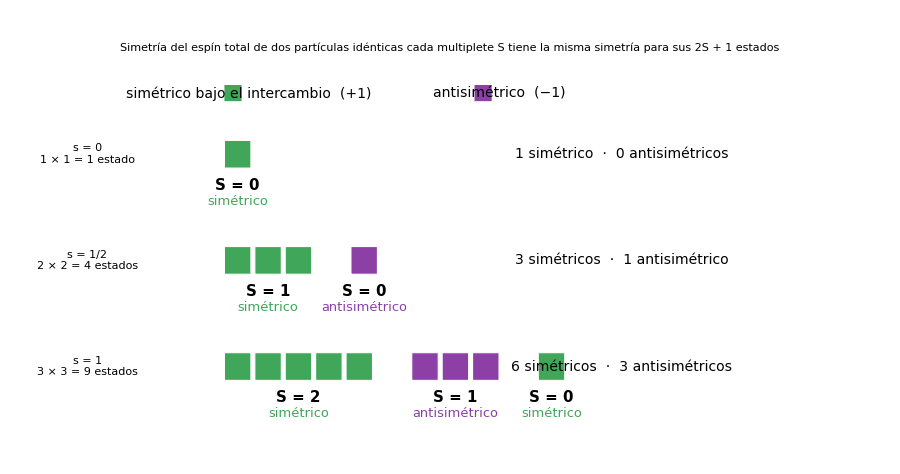

```mathematica
(* ==================================================================*)(*BoletinA_P12_c-Simetria del espin total para s=0,1/2 y 1*)(* ==================================================================*)bloqueS[x0_,y_,S_,sgn_]:=Module[{col=If[sgn>0,eSim,eAnt],n=2 S+1,w=0.62},{Table[{col,EdgeForm[White],Rectangle[{x0+(k-1) w,y-0.3},{x0+(k-1) w+0.54,y+0.3}]},{k,n}],Text[Style["S = "<>ToString[S],15,Bold],{x0+(n w-0.08)/2,y-0.68}],Text[Style[If[sgn>0,"simétrico","antisimétrico"],13,col],{x0+(n w-0.08)/2,y-1.02}]}];

resumenS[y_,ns_,na_]:=Text[Style[Row[{Style[ToString[ns],eSim,Bold],If[ns==1," simétrico  ·  "," simétricos  ·  "],Style[ToString[na],eAnt,Bold],If[na==1," antisimétrico"," antisimétricos"]}],14],{11.0,y},{-1,0}];

fMc=Graphics[{(*leyenda*){eSim,Rectangle[{2.9,6.95},{3.25,7.3}]},Text[Style["simétrico bajo el intercambio  (+1)",14],{3.4,7.12},{-1,0}],{eAnt,Rectangle[{8.0,6.95},{8.35,7.3}]},Text[Style["antisimétrico  (−1)",14],{8.5,7.12},{-1,0}],(*s=0*)Text[Column[{Style["s = 0",18,Bold],Style["1 × 1 = 1 estado",13,eGris]},Left],{0.1,5.8},{-1,0}],bloqueS[2.9,5.8,0,1],resumenS[5.8,1,0],(*s=1/2*)Text[Column[{Style["s = 1/2",18,Bold],Style["2 × 2 = 4 estados",13,eGris]},Left],{0.1,3.5},{-1,0}],bloqueS[2.9,3.5,1,1],bloqueS[5.48,3.5,0,-1],resumenS[3.5,3,1],(*s=1*)Text[Column[{Style["s = 1",18,Bold],Style["3 × 3 = 9 estados",13,eGris]},Left],{0.1,1.2},{-1,0}],bloqueS[2.9,1.2,2,1],bloqueS[6.72,1.2,1,-1],bloqueS[9.3,1.2,0,1],resumenS[1.2,6,3]},PlotRange->{{0,15},{-0.2,7.7}},PlotRangePadding->None,ImageSize->900,PlotLabel->Column[{Style["Simetría del espín total de dos partículas idénticas",20,Bold],Style["cada multiplete S tiene la misma simetría para sus 2S + 1 estados",14,eGris]},Center]]
```

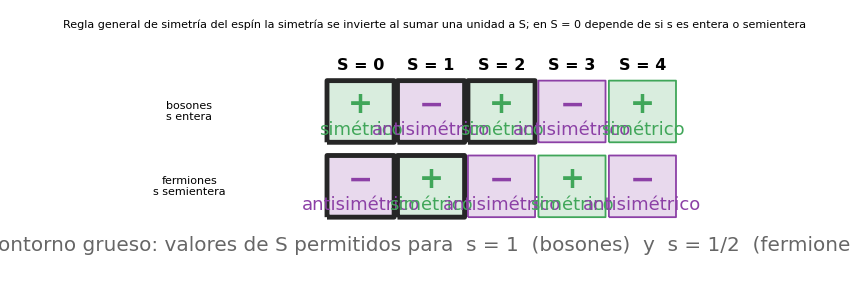

```mathematica
(* ==================================================================*)
(*BoletinA_P12_d-Regla general:la simetria alterna con S*)
(* ==================================================================*)
celdaRegla[fila_,S_,signo_,destacada_]:=Module[{col=If[signo>0,eSim,eAnt],x1=4.2+2.1 S,y1=If[fila==1,2.0,0.3]},{{Lighter[col,0.8],EdgeForm[{If[destacada,GrayLevel[0.15],col],AbsoluteThickness[If[destacada,3.5,1.3]]}],Rectangle[{x1,y1},{x1+2.0,y1+1.4},RoundingRadius->0.1]},Text[Style[If[signo>0,"+","−"],30,Bold,col],{x1+1.0,y1+0.85}],Text[Style[If[signo>0,"simétrico","antisimétrico"],18,col],{x1+1.0,y1+0.28}]}];

fMd=Graphics[{
(*cabeceras de columna*)
Table[Text[Style["S = "<>ToString[S],16,Bold],{4.2+2.1 S+1.0,3.75}],{S,0,4}],
(*bosones:(-1)^S;fermiones:-(-1)^S*)
Text[Column[{Style["bosones",18,Bold],Style["s entera",20,eGris]},Left],{0.1,2.7},{-1,0}],Table[celdaRegla[1,S,(-1)^S,S<=2],{S,0,4}],Text[Column[{Style["fermiones",18,Bold],Style["s semientera",20,eGris]},Left],{0.1,1.0},{-1,0}],Table[celdaRegla[2,S,-(-1)^S,S<=1],{S,0,4}],Text[Style["contorno grueso: valores de S permitidos para  s = 1  (bosones)  y  s = 1/2  (fermiones)",20,eGris],{7.2,-0.35}]},
PlotRange->{{0,14.8},{-0.8,4.3}},
PlotRangePadding->None,
ImageSize->850,
PlotLabel->Column[{Style["Regla general de simetría del espín",24,Bold],
Style["la simetría se invierte al sumar una unidad a S; en S = 0 depende de si s es entera o semientera",18,eGris]},Center]]
```

```mathematica
(*----------Exportar----------*)
Export["BoletinA_P12_a.png",fMa,"PNG",Background->None,ImageResolution->300,ImageSize->850];
Export["BoletinA_P12_b.png",fMb,"PNG",Background->None,ImageResolution->300,ImageSize->900];
Export["BoletinA_P12_c.png",fMc,"PNG",Background->None,ImageResolution->300,ImageSize->900];
Export["BoletinA_P12_d.png",fMd,"PNG",Background->None,ImageResolution->300,ImageSize->850];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["BoletinA_P12_a.png"]]]
```